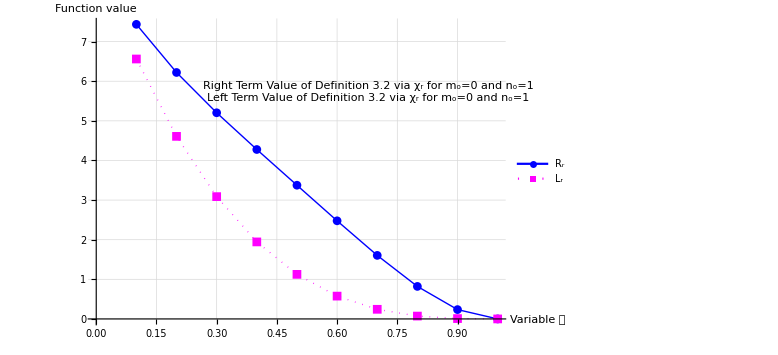
{0.231071,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,7.4358},{0.2,6.2208000000000006},{0.3,5.203799999999999},{0.4,4.2768},{0.5,3.375},{0.6,2.4767999999999994},{0.7,1.6037999999999994},{0.8,0.8207999999999995},{0.9,0.23579999999999987},{1.0,0.}};
data2={{0.1,6.561000000000001},{0.2,4.608000000000001},{0.3,3.087},{0.4,1.944},{0.5,1.125},{0.6,0.5759999999999996},{0.7,0.2429999999999998},{0.8,0.07199999999999995},{0.9,0.008999999999999994},{1.0,0.}};

ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Dotted,Thick}},PlotLegends->Placed[{"R_r","L_r"},{0.9,0.9}],AxesLabel->{"Variable 𝔅","Function value"},ImageSize->Large,GridLines->Automatic,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via χ_r for m_o=0 and n_o=1",Blue],Style["Left Term Value of Definition 3.2 via χ_r for m_o=0 and n_o=1",Magenta]}],RoundingRadius->5],Scaled[{0.67,0.76}]]]]
```

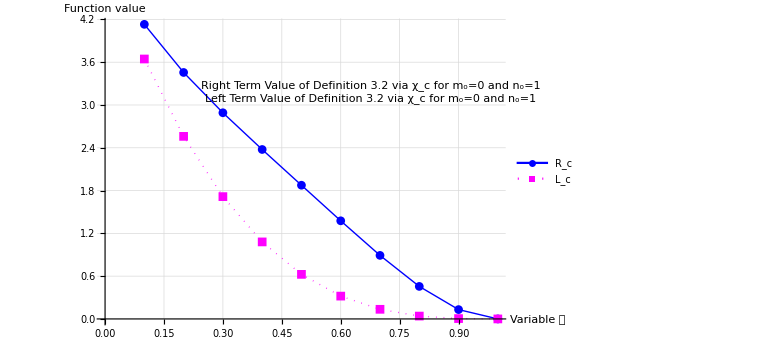
{0.108632,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,4.131},{0.2,3.456},{0.3,2.891},{0.4,2.376},{0.5,1.875},{0.6,1.3759999999999994},{0.7,0.8909999999999998},{0.8,0.4559999999999998},{0.9,0.13099999999999992},{1.0,0.}};
data2={{0.1,3.6450000000000005},{0.2,2.5600000000000005},{0.3,1.7149999999999996},{0.4,1.08},{0.5,0.625},{0.6,0.3199999999999998},{0.7,0.1349999999999999},{0.8,0.03999999999999997},{0.9,0.004999999999999997},{1.0,0.}};

ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Dotted,Thick}},PlotLegends->Placed[{"R_c","L_c"},{0.9,0.9}],AxesLabel->{"Variable 𝔅","Function value"},ImageSize->Large,GridLines->Automatic,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via χ_c for m_o=0 and n_o=1",Blue],Style["Left Term Value of Definition 3.2 via χ_c for m_o=0 and n_o=1",Magenta]}],RoundingRadius->5],Scaled[{0.67,0.76}]]]]
```

```mathematica
AbsoluteTiming [Plot3D[{9(a^3+b^3)/2-9/10 (b-a)^3,(9 (-a^4/4+b^4/4))/(-a+b),9((a+b)/2)^3+9(b-a)^3/32},{a,0,0.5},{b,0.6,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{{Blue,Thick},{Green,Dashed,Thick},{Magenta,Dotted,Thick}},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["",15,Bold,Red],Style["",15,Bold,Red],Style["",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"R_r","M_r","L_r"},{0.1,0.1}]]]
```

{2.28243,-Graphics-}

```mathematica
AbsoluteTiming [Plot3D[{5(a^3+b^3)/2-5/10 (b-a)^3,(5 (-a^4/4+b^4/4))/(-a+b),5((a+b)/2)^3+5(b-a)^3/32},{a,0,0.5},{b,0.6,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{{Blue,Thick},{Green,Dashed,Thick},{Magenta,Dotted,Thick}},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["",15,Bold,Red],Style["",15,Bold,Red],Style["",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"R_c","M_c","L_c"},{0.1,0.1}]]]
```

{0.158004,-Graphics-}

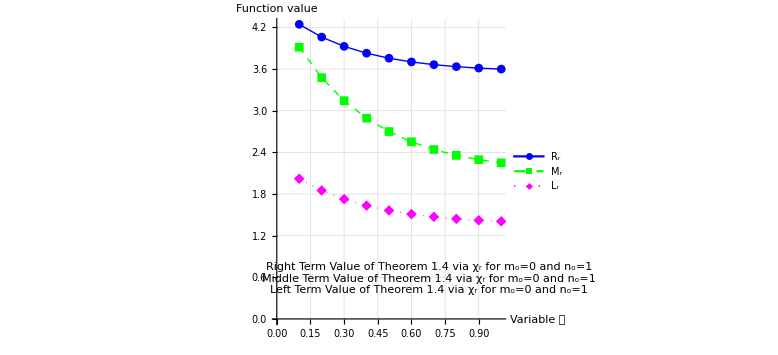
{0.118007,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,4.245266535195725},{0.2,4.061688311688312},{0.3,3.927902734272805},{0.4,3.829640947288006},{0.5,3.757142857142857},{0.6,3.7035953177257523},{0.7,3.6641579000778},{0.8,3.6353383458646613},{0.9,3.6145825913780283},{1.0,3.6}};
data2={{0.1,3.9155844155844157},{0.2,3.477272727272727},{0.3,3.1454849498327757},{0.4,2.8928571428571432},{0.5,2.7},{0.6,2.5528846153846154},{0.7,2.4411764705882355},{0.8,2.3571428571428568},{0.9,2.29491833030853},{1.0,2.25}};
data3={{0.1,2.0200663853856864},{0.2,1.8513769654945165},{0.3,1.7263258691404864},{0.4,1.6329732864097677},{0.5,1.5630241177918776},{0.6,1.5105955126680715},{0.7,1.4714405458445614},{0.8,1.4424453788758347},{0.9,1.4212955871431885},{1.0,1.40625}};

ListLinePlot[{data1,data2,data3},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Green,Dashed,Thick},{Magenta,Dotted,Thick}},PlotLegends->Placed[{"R_r","M_r","L_r"},{0.1,0.15}],AxesLabel->{"Variable 𝔅","Function value"},ImageSize->Large,GridLines->Automatic,Epilog->Inset[Framed[Column[{Style["Right Term Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Blue],Style["Middle Term Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Green],Style["Left Term Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Magenta]}],RoundingRadius->5],Scaled[{0.67,0.15}]]]]
```

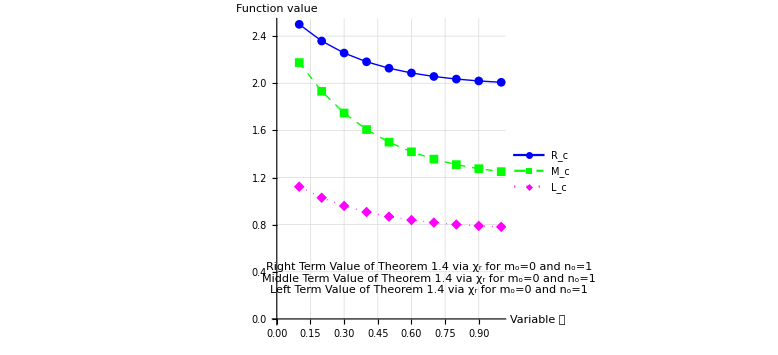
{0.0780251,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,2.5},{0.2,2.3584814084420693},{0.3,2.2564935064935066},{0.4,2.1821681857071136},{0.5,2.1275783040488925},{0.6,2.0873015873015874},{0.7,2.0575529542920847},{0.8,2.035643277821},{0.9,2.0196324143692563},{1.0,2.0081014396544603}};
data2={{0.1,2.175324675324675},{0.2,1.9318181818181817},{0.3,1.7474916387959865},{0.4,1.6071428571428572},{0.5,1.5},{0.6,1.4182692307692308},{0.7,1.3562091503267977},{0.8,1.3095238095238093},{0.9,1.2749546279491835},{1.0,1.25}};
data3={{0.1,1.122259102992048},{0.2,1.0285427586080647},{0.3,0.9590699273002703},{0.4,0.9072073813387599},{0.5,0.8683467321065987},{0.6,0.8392197292600396},{0.7,0.8174669699136452},{0.8,0.8013585438199081},{0.9,0.7896086595239935},{1.0,0.78125}};

ListLinePlot[{data1,data2,data3},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Green,Dashed,Thick},{Magenta,Dotted,Thick}},PlotLegends->Placed[{"R_c","M_c","L_c"},{0.1,0.15}],AxesLabel->{"Variable 𝔅","Function value"},ImageSize->Large,GridLines->Automatic,Epilog->Inset[Framed[Column[{Style["Right Term Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Blue],Style["Middle Term Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Green],Style["Left Term Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Magenta]}],RoundingRadius->5],Scaled[{0.67,0.15}]]]]
```

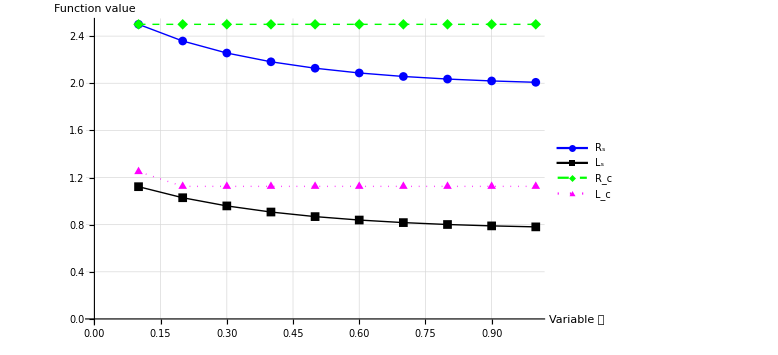
{0.0640024,-Graphics-}

```mathematica
AbsoluteTiming [data1={{0.1,2.5},{0.2,2.3584814084420693},{0.3,2.2564935064935066},{0.4,2.1821681857071136},{0.5,2.1275783040488925},{0.6,2.0873015873015874},{0.7,2.0575529542920847},{0.8,2.035643277821},{0.9,2.0196324143692563},{1.0,2.0081014396544603}};
data2={{0.1,1.122259102992048},{0.2,1.0285427586080647},{0.3,0.9590699273002703},{0.4,0.9072073813387599},{0.5,0.8683467321065987},{0.6,0.8392197292600396},{0.7,0.8174669699136452},{0.8,0.8013585438199081},{0.9,0.7896086595239935},{1.0,0.78125}};
data3={{0.1,2.5},{0.2,2.5},{0.3,2.5},{0.4,2.5},{0.5,2.5},{0.6,2.5},{0.7,2.5},{0.8,2.5},{0.9,2.5},{1.0,2.5}};
data4={{0.1,1.25},{0.2,1.125},{0.3,1.125},{0.4,1.125},{0.5,1.125},{0.6,1.125},{0.7,1.125},{0.8,1.125},{0.9,1.125},{1.0,1.125}};


ListLinePlot[{data1,data2,data3, data4},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Black,Thick},{Green,Dashed,Thick},{Magenta,Dotted,Thick}},PlotLegends->Placed[{"R_s","L_s","R_c","L_c"},{0.9,0.8}],AxesLabel->{"Variable 𝔅","Function value"},ImageSize->Large,GridLines->Automatic]]
```

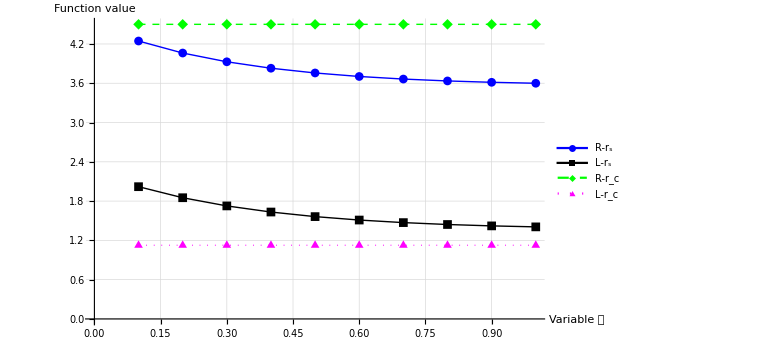
{0.0893746,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,4.245266535195725},{0.2,4.061688311688312},{0.3,3.927902734272805},{0.4,3.829640947288006},{0.5,3.757142857142857},{0.6,3.7035953177257523},{0.7,3.6641579000778},{0.8,3.6353383458646613},{0.9,3.6145825913780283},{1.0,3.6}};
data2={{0.1,2.0200663853856864},{0.2,1.8513769654945165},{0.3,1.7263258691404864},{0.4,1.6329732864097677},{0.5,1.5630241177918776},{0.6,1.5105955126680715},{0.7,1.4714405458445614},{0.8,1.4424453788758347},{0.9,1.4212955871431885},{1.0,1.40625}};
data3={{0.1,9/2},{0.2,9/2},{0.3,9/2},{0.4,9/2},{0.5,9/2},{0.6,9/2},{0.7,9/2},{0.8,9/2},{0.9,9/2},{1.0,9/2}};
data4={{0.1,1.125},{0.2,1.125},{0.3,1.125},{0.4,1.125},{0.5,1.125},{0.6,1.125},{0.7,1.125},{0.8,1.125},{0.9,1.125},{1.0,1.125}};
ListLinePlot[{data1,data2,data3, data4},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Black,Thick},{Green,Dashed,Thick},{Magenta,Dotted,Thick}},PlotLegends->Placed[{"R-r_s","L-r_s","R-r_c","L-r_c"},{0.9,0.6}],AxesLabel->{"Variable 𝔅","Function value"},ImageSize->Large,GridLines->Automatic]]
```

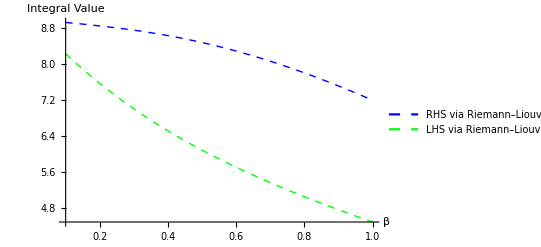
{2.77249,-Graphics-}

```mathematica
AbsoluteTiming [Plot[{NIntegrate[(1-t)^(β-1)*(t(0-9(1-t)^3)+(1-t) (9-9(t^3)))/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*(t(0-9(1-t)^3)+(1-t) (9-9(t^3)))/Gamma[β],{t,0,1}],NIntegrate[(1-t)^(β-1)*9(1-t)^3/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*9(1-t)^3/Gamma[β],{t,0,1}]},{β,0.1,1},PlotStyle->{{Blue,Dashed,Thick},{{Green,Dashed,Thick}}},PlotLegends->Placed[{"RHS via Riemann–Liouville","LHS via Riemann–Liouville" },{0.9,0.6}],AxesLabel->{"β","Integral Value"}]]
```

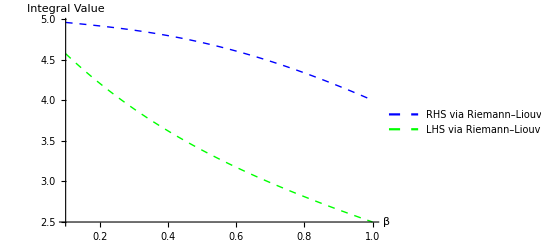
{2.68702,-Graphics-}

```mathematica
AbsoluteTiming [Plot[{NIntegrate[(1-t)^(β-1)*(t(0-5(1-t)^3)+(1-t) (5-5(t^3)))/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*(t(0-5(1-t)^3)+(1-t) (5-5(t^3)))/Gamma[β],{t,0,1}],NIntegrate[(1-t)^(β-1)*(5(1-t)^3)/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*(5(1-t)^3)/Gamma[β],{t,0,1}]},{β,0.1,1},PlotStyle->{{Blue,Dashed,Thick},{{Green,Dashed,Thick}}},PlotLegends->Placed[{"RHS via Riemann–Liouville","LHS via Riemann–Liouville"},{0.9,0.6}],AxesLabel->{"β","Integral Value"}]]
```

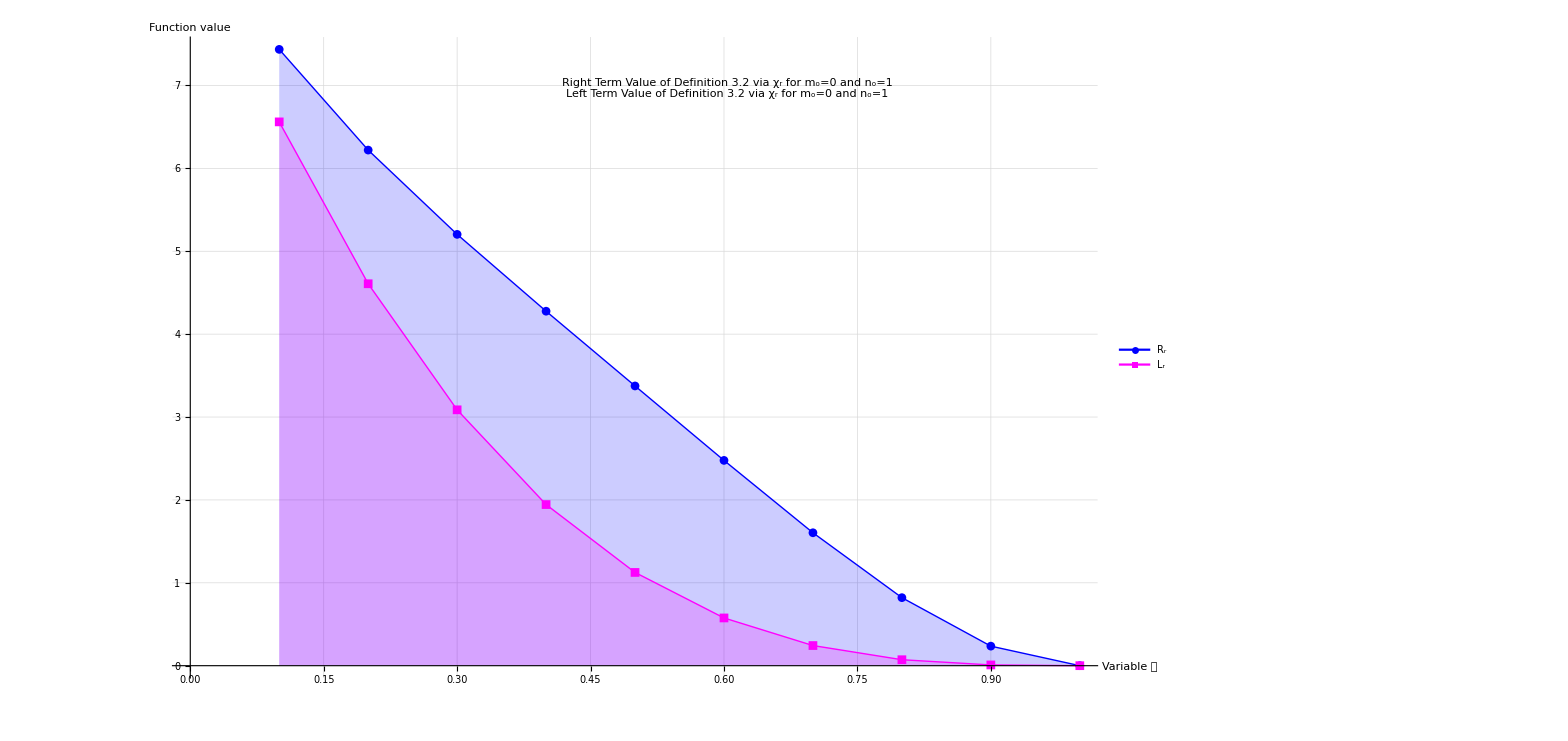
{0.317326,-Graphics-}

```mathematica
AbsoluteTiming [data1={{0.1,7.4358},{0.2,6.2208},{0.3,5.2038},{0.4,4.2768},{0.5,3.375},{0.6,2.4768},{0.7,1.6038},{0.8,0.8208},{0.9,0.2358},{1.0,0.}};
data2={{0.1,6.561},{0.2,4.608},{0.3,3.087},{0.4,1.944},{0.5,1.125},{0.6,0.576},{0.7,0.243},{0.8,0.072},{0.9,0.009},{1.0,0.}};

plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]]
```

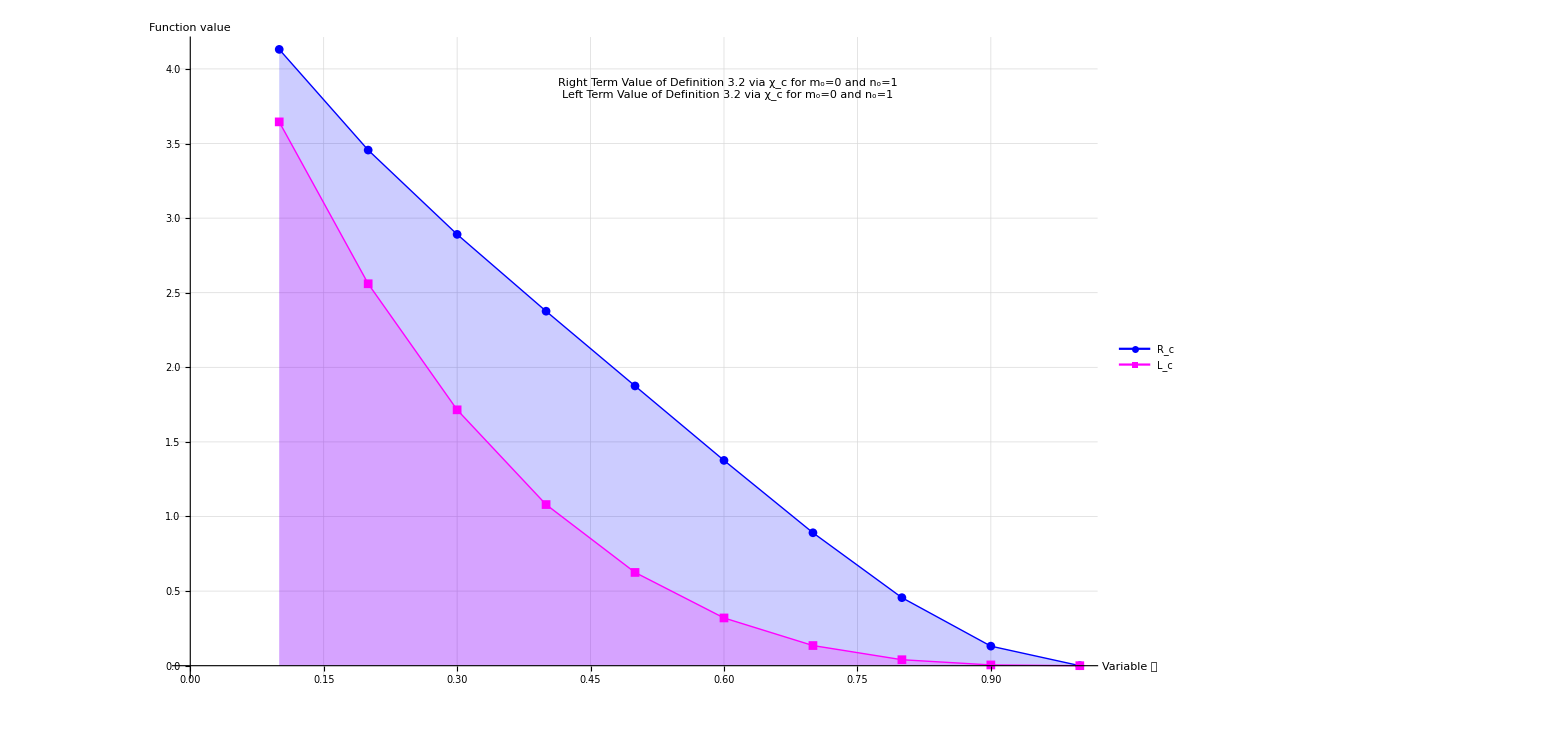
{0.0955507,-Graphics-}

```mathematica
AbsoluteTiming [data1={{0.1,4.131},{0.2,3.456},{0.3,2.891},{0.4,2.376},{0.5,1.875},{0.6,1.3759999999999994},{0.7,0.8909999999999998},{0.8,0.4559999999999998},{0.9,0.13099999999999992},{1.0,0.}};
data2={{0.1,3.6450000000000005},{0.2,2.5600000000000005},{0.3,1.7149999999999996},{0.4,1.08},{0.5,0.625},{0.6,0.3199999999999998},{0.7,0.1349999999999999},{0.8,0.03999999999999997},{0.9,0.004999999999999997},{1.0,0.}};

plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","c"],FontSize->40],Style[Subscript["L","c"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(c\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(c\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]]
```

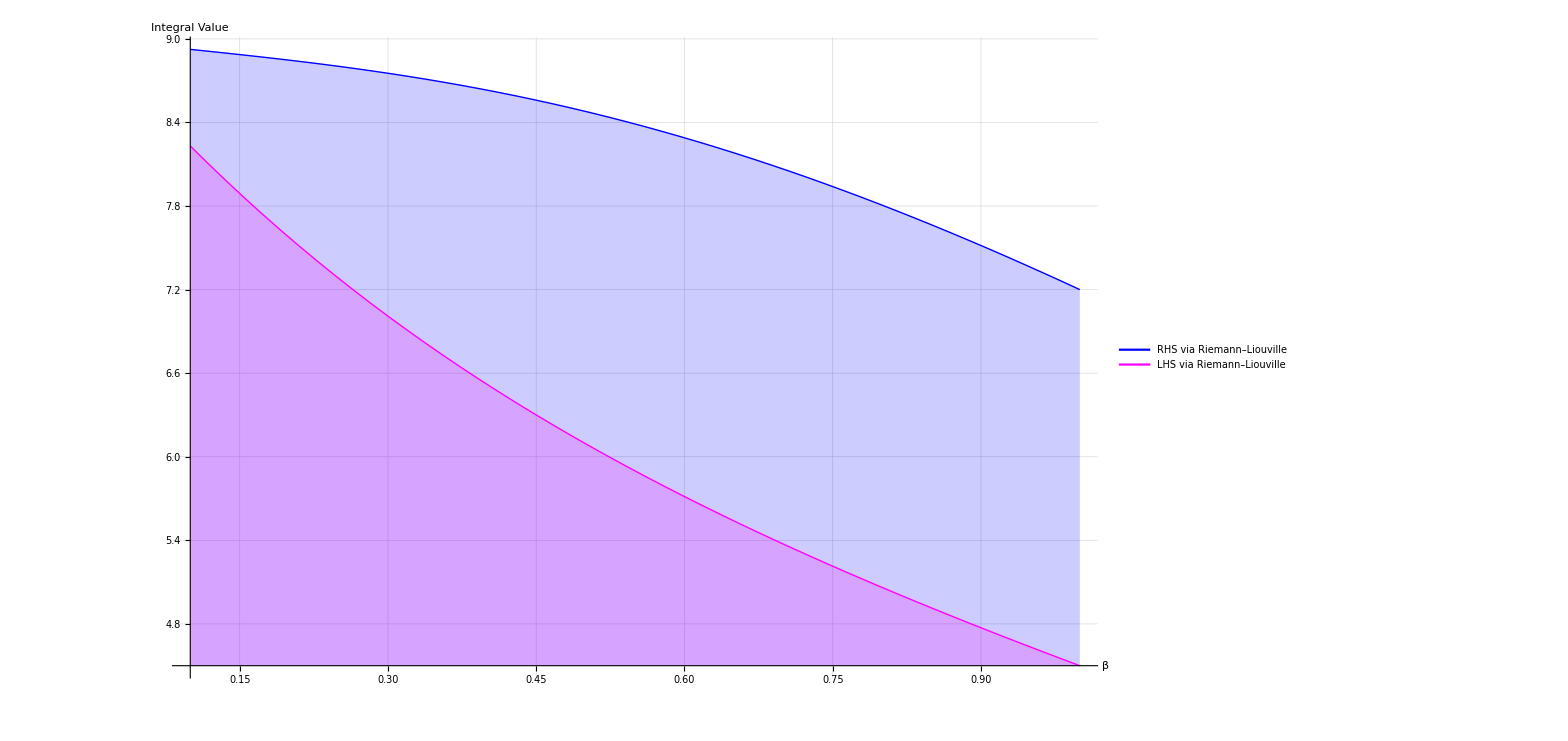
{3.15776,-Graphics-}

```mathematica
AbsoluteTiming [Plot[{NIntegrate[(1-t)^(β-1)*(t(0-9(1-t)^3)+(1-t) (9-9(t^3)))/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*(t(0-9(1-t)^3)+(1-t) (9-9(t^3)))/Gamma[β],{t,0,1}],NIntegrate[(1-t)^(β-1)*9(1-t)^3/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*9(1-t)^3/Gamma[β],{t,0,1}]},{β,0.1,1},PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{"RHS via Riemann–Liouville","LHS via Riemann–Liouville" },{0.9,0.6}],AxesLabel->{"β","Integral Value"},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis]]
```

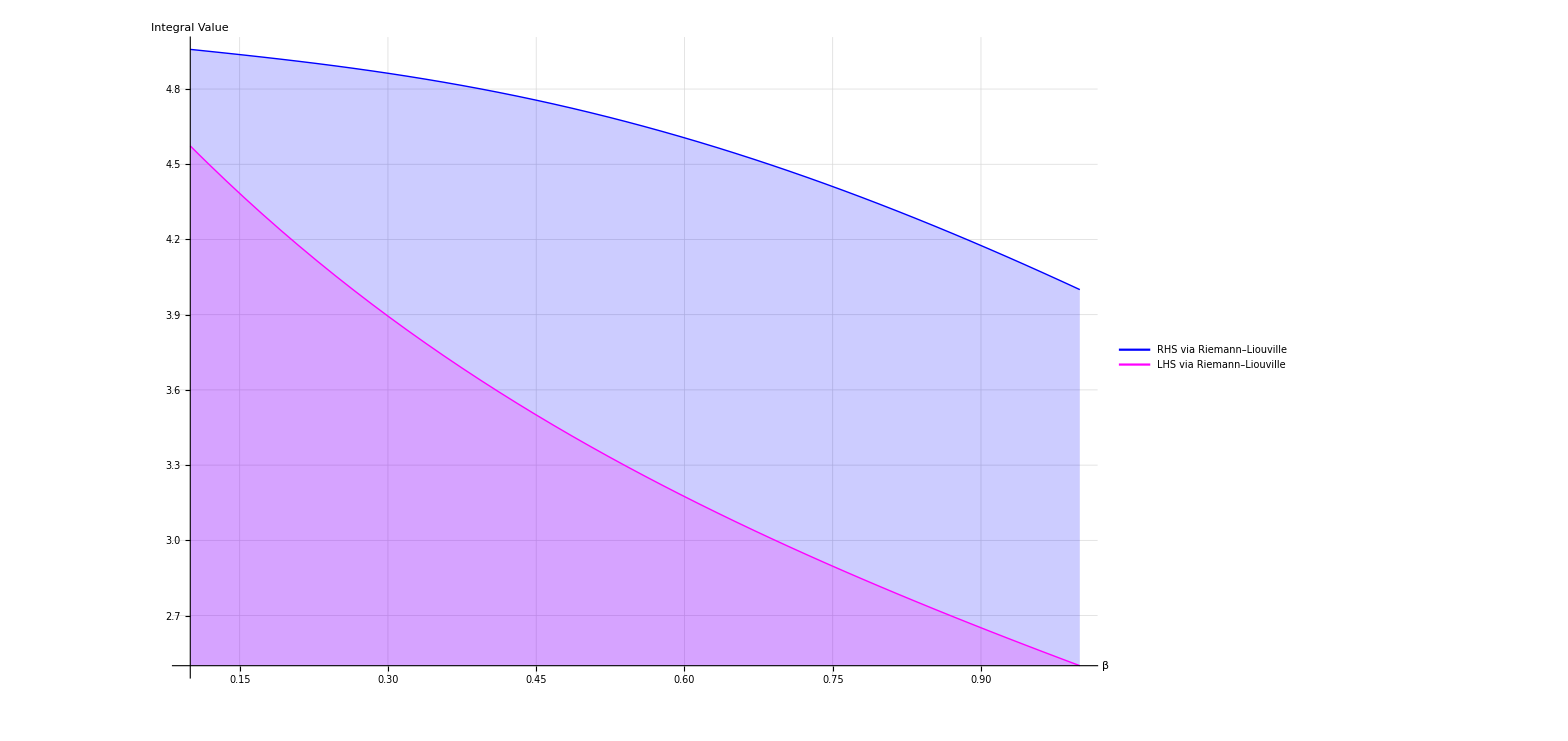
{2.73544,-Graphics-}

```mathematica
AbsoluteTiming [Plot[{NIntegrate[(1-t)^(β-1)*(t(0-5(1-t)^3)+(1-t) (5-5(t^3)))/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*(t(0-5(1-t)^3)+(1-t) (5-5(t^3)))/Gamma[β],{t,0,1}],NIntegrate[(1-t)^(β-1)*(5(1-t)^3)/Gamma[β],{t,0,1}]+NIntegrate[(t-0)^(β-1)*(5(1-t)^3)/Gamma[β],{t,0,1}]},{β,0.1,1},PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{"RHS via Riemann–Liouville","LHS via Riemann–Liouville" },{0.9,0.6}],AxesLabel->{"β","Integral Value"},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis]]
```

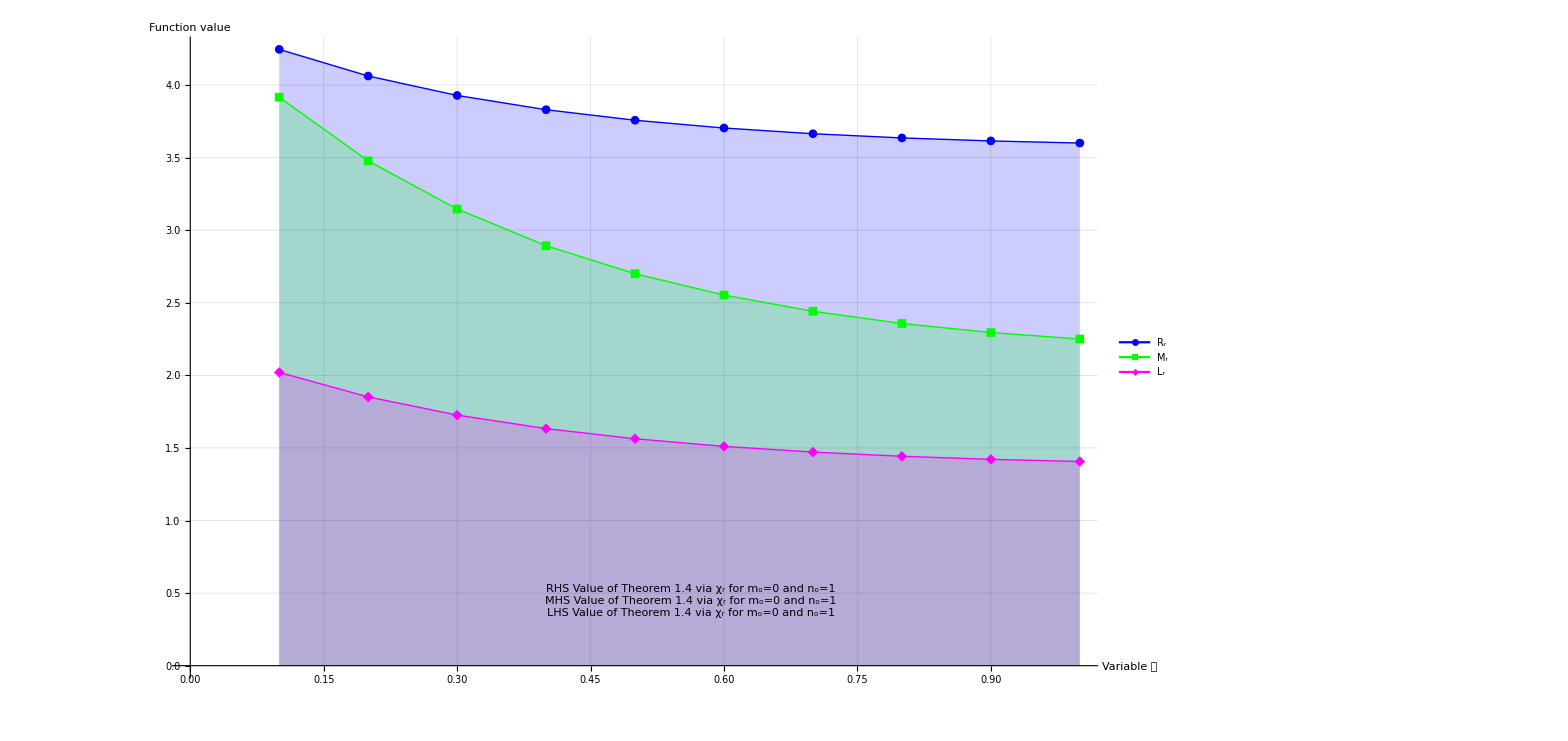
{0.0593997,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,4.245266535195725},{0.2,4.061688311688312},{0.3,3.927902734272805},{0.4,3.829640947288006},{0.5,3.757142857142857},{0.6,3.7035953177257523},{0.7,3.6641579000778},{0.8,3.6353383458646613},{0.9,3.6145825913780283},{1.0,3.6}};
data2={{0.1,3.9155844155844157},{0.2,3.477272727272727},{0.3,3.1454849498327757},{0.4,2.8928571428571432},{0.5,2.7},{0.6,2.5528846153846154},{0.7,2.4411764705882355},{0.8,2.3571428571428568},{0.9,2.29491833030853},{1.0,2.25}};
data3={{0.1,2.0200663853856864},{0.2,1.8513769654945165},{0.3,1.7263258691404864},{0.4,1.6329732864097677},{0.5,1.5630241177918776},{0.6,1.5105955126680715},{0.7,1.4714405458445614},{0.8,1.4424453788758347},{0.9,1.4212955871431885},{1.0,1.40625}};
ListLinePlot[{data1,data2,data3},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Green,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["M","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*Ensures large visual size*)GridLines->Automatic,LabelStyle->Directive[Black,FontSize->16],Filling->Axis,Epilog->Inset[Framed[Column[{Style["RHS Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Blue,28],Style["MHS Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Green,28], Style["LHS Value of Theorem 1.4 via χ_r for m_o=0 and n_o=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.56,0.12}]]]]
```

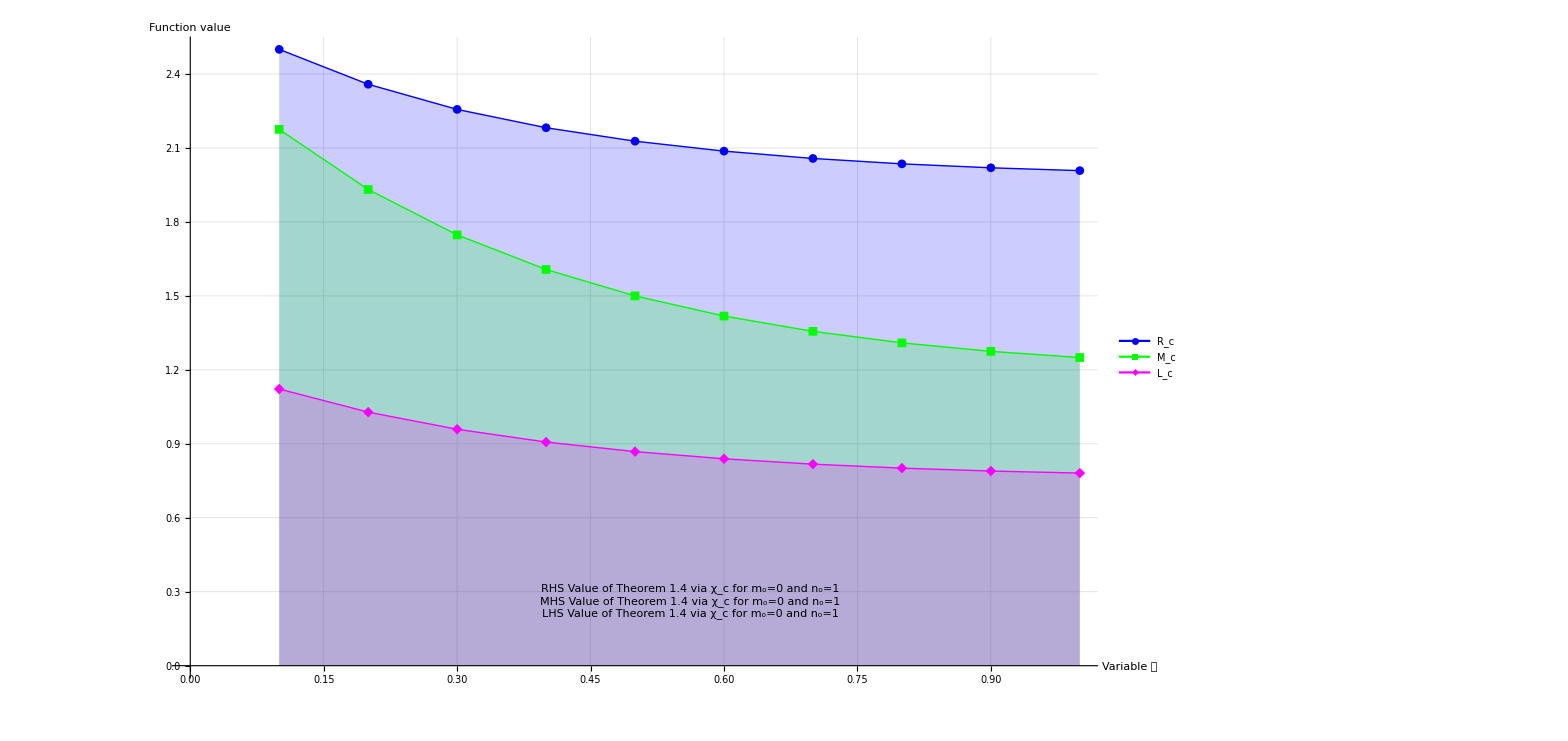
{0.0901155,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,2.5},{0.2,2.3584814084420693},{0.3,2.2564935064935066},{0.4,2.1821681857071136},{0.5,2.1275783040488925},{0.6,2.0873015873015874},{0.7,2.0575529542920847},{0.8,2.035643277821},{0.9,2.0196324143692563},{1.0,2.0081014396544603}};
data2={{0.1,2.175324675324675},{0.2,1.9318181818181817},{0.3,1.7474916387959865},{0.4,1.6071428571428572},{0.5,1.5},{0.6,1.4182692307692308},{0.7,1.3562091503267977},{0.8,1.3095238095238093},{0.9,1.2749546279491835},{1.0,1.25}};
data3={{0.1,1.122259102992048},{0.2,1.0285427586080647},{0.3,0.9590699273002703},{0.4,0.9072073813387599},{0.5,0.8683467321065987},{0.6,0.8392197292600396},{0.7,0.8174669699136452},{0.8,0.8013585438199081},{0.9,0.7896086595239935},{1.0,0.78125}};
ListLinePlot[{data1,data2,data3},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Green,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","c"],FontSize->40],Style[Subscript["M","c"],FontSize->40],Style[Subscript["L","c"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*Ensures large visual size*)GridLines->Automatic,LabelStyle->Directive[Black,FontSize->16],Filling->Axis,Epilog->Inset[Framed[Column[{Style["RHS Value of Theorem 1.4 via χ_c for m_o=0 and n_o=1",Blue,28],Style["MHS Value of Theorem 1.4 via χ_c for m_o=0 and n_o=1",Green,28], Style["LHS Value of Theorem 1.4 via χ_c for m_o=0 and n_o=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.56,0.12}]]]]
```

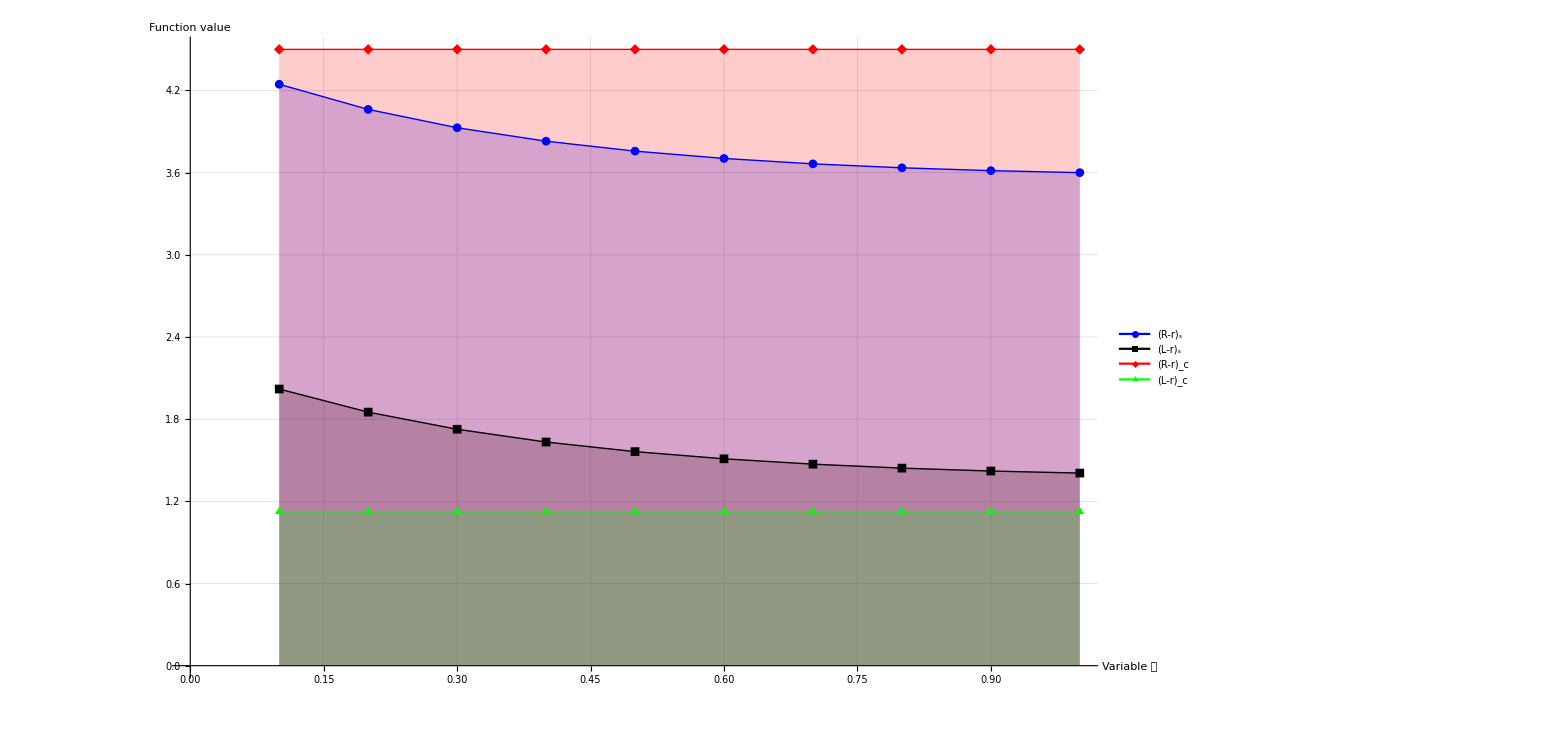
{0.088678,-Graphics-}

```mathematica
AbsoluteTiming [(*Sample data placeholders—replace with actual numerical data*)data1={{0.1,4.245266535195725},{0.2,4.061688311688312},{0.3,3.927902734272805},{0.4,3.829640947288006},{0.5,3.757142857142857},{0.6,3.7035953177257523},{0.7,3.6641579000778},{0.8,3.6353383458646613},{0.9,3.6145825913780283},{1.0,3.6}};
data2={{0.1,2.0200663853856864},{0.2,1.8513769654945165},{0.3,1.7263258691404864},{0.4,1.6329732864097677},{0.5,1.5630241177918776},{0.6,1.5105955126680715},{0.7,1.4714405458445614},{0.8,1.4424453788758347},{0.9,1.4212955871431885},{1.0,1.40625}};
data3={{0.1,9/2},{0.2,9/2},{0.3,9/2},{0.4,9/2},{0.5,9/2},{0.6,9/2},{0.7,9/2},{0.8,9/2},{0.9,9/2},{1.0,9/2}};
data4={{0.1,1.125},{0.2,1.125},{0.3,1.125},{0.4,1.125},{0.5,1.125},{0.6,1.125},{0.7,1.125},{0.8,1.125},{0.9,1.125},{1.0,1.125}};
ListLinePlot[{data1,data2,data3, data4},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Black,Thick},{Red,Thick},{Green,Thick}},PlotLegends->Placed[{Style[Subscript["R-r","s"],FontSize->40],Style[Subscript["L-r","s"],FontSize->40],Style[Subscript["R-r","c"],FontSize->40], Style[Subscript["L-r","c"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},(*Ensures large visual size*)GridLines->Automatic,ImageSize->1200,(*Ensures large visual size*)GridLines->Automatic,LabelStyle->Directive[Black,FontSize->16],Filling->Axis,LabelStyle->Directive[Black,FontSize->16]]]
```

```mathematica
AbsoluteTiming [
```